```mathematica
ClearAll["`*"];
```

#### 0. Set parameters

```mathematica
(*This note is modified from

Deng,X.-L.,& Sneeuw,N.(2023).Analytical Solutions for Gravitational Potential up to Its Third-order Derivatives of a Tesseroid,Spherical Zonal Band,and Spherical Shell.Surveys in Geophysics,44(4),1125–1173. https://doi.org/10.1007/s10712-023-09774-z

 and is used to calculate the analytical expression and reference value of a single tesseroid in the Arctic gravitational field*)
```

```mathematica
φ=Pi/2;(*φ=Pi/2-θ, θ=0*)
```

```mathematica
φ3=Pi/2-θ3;
```

```mathematica
cosPhi=Sin[φ]*Sin[φ3]+Cos[φ]*Cos[φ3]*Cos[λ3-λ]
```

Cos[θ3]

```mathematica
TrigToExp[ArcTanh[(r3-r Cos[θ3])/(√(r^2+r3^2-2 r r3 Cos[θ3]))]]
```

-1/2 Log[1-(-1/2 (ⅇ^(-ⅈ θ3)+ⅇ^(ⅈ θ3)) r+r3)/(√(r^2-(ⅇ^(-ⅈ θ3)+ⅇ^(ⅈ θ3)) r r3+r3^2))]+1/2 Log[1+(-1/2 (ⅇ^(-ⅈ θ3)+ⅇ^(ⅈ θ3)) r+r3)/(√(r^2-(ⅇ^(-ⅈ θ3)+ⅇ^(ⅈ θ3)) r r3+r3^2))]

```mathematica
1/2 Log[(l-Cos[θ3] r+r3)/(l+Cos[θ3] r-r3)];
```

```mathematica
V[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=(G ρ (λ2-λ1))/(12 r)(√(r^2+r1^2-2 r r1 Cos[θ1]) (r^2+4 r1^2-2 r r1 Cos[θ1]-3 r^2 Cos[2 θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]) (-r^2-4 r2^2+2 r r2 Cos[θ1]+3 r^2 Cos[2 θ1])+√(r^2+r2^2-2 r r2 Cos[θ2]) (r^2+4 r2^2-2 r r2 Cos[θ2]-3 r^2 Cos[2 θ2])+√(r^2+r1^2-2 r r1 Cos[θ2]) (-r^2-4 r1^2+2 r r1 Cos[θ2]+3 r^2 Cos[2 θ2])+6 r^3 Cos[θ1] Log[(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))/(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))] Sin[θ1]^2+6 r^3 Cos[θ2] Log[(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))/(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))] Sin[θ2]^2)
```

```mathematica
Vz[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=-(G ρ(λ2-λ1))/(3 r^2)(√(r^2+r1^2-2 r r1 Cos[θ1]) (-2 r^2+r1^2+r Cos[θ1] (r1+3 r Cos[θ1]))-√(r^2+r2^2-2 r r2 Cos[θ1]) (-2 r^2+r2^2+r Cos[θ1] (r2+3 r Cos[θ1]))-√(r^2+r1^2-2 r r1 Cos[θ2]) (-2 r^2+r1^2+r Cos[θ2] (r1+3 r Cos[θ2]))+√(r^2+r2^2-2 r r2 Cos[θ2]) (-2 r^2+r2^2+r Cos[θ2] (r2+3 r Cos[θ2]))+3 r^3 Cos[θ1] Log[(r2-r1+√(r^2+r2^2-2 r r2 Cos[θ1])+√(r^2+r1^2-2 r r1 Cos[θ1]))/(r1-r2+√(r^2+r2^2-2 r r2 Cos[θ1])+√(r^2+r1^2-2 r r1 Cos[θ1]))] Sin[θ1]^2+3 r^3 Cos[θ2] Log[(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))/(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))] Sin[θ2]^2)
```

```mathematica
Vzz[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=(G ρ(λ2-λ1))/(6 r^3)((r^4+r^2 r1^2+4 r1^4-r r1 (r^2+4 r1^2) Cos[θ1]-r^2 (3 r^2+r1^2) Cos[2 θ1]+3 r^3 r1 Cos[3 θ1])/(√(r^2+r1^2-2 r r1 Cos[θ1]))-(r^4+r^2 r2^2+4 r2^4-r r2 (r^2+4 r2^2) Cos[θ1]-r^2 (3 r^2+r2^2) Cos[2 θ1]+3 r^3 r2 Cos[3 θ1])/(√(r^2+r2^2-2 r r2 Cos[θ1]))-(r^4+r^2 r1^2+4 r1^4-r r1 (r^2+4 r1^2) Cos[θ2]-r^2 (3 r^2+r1^2) Cos[2 θ2]+3 r^3 r1 Cos[3 θ2])/(√(r^2+r1^2-2 r r1 Cos[θ2]))+(r^4+r^2 r2^2+4 r2^4-r r2 (r^2+4 r2^2) Cos[θ2]-r^2 (3 r^2+r2^2) Cos[2 θ2]+3 r^3 r2 Cos[3 θ2])/(√(r^2+r2^2-2 r r2 Cos[θ2]))+6 r^3 Cos[θ1] Log[(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))/(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))] Sin[θ1]^2+6 r^3 Cos[θ2] Log[(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))/(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))] Sin[θ2]^2)
```

```mathematica
Vxx[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=(G ρ)/48(-3 Cos[θ1] Log[(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))/(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))] (8 (-λ1+λ2) Sin[θ1]^2+4 (-5+Cos[2 θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2])-3 Cos[θ2]Log[(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))/(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))] (8 (-λ1+λ2) Sin[θ2]^2+4 (-5+Cos[2 θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2])+(4 (r^4+r^2 r1^2+4 r1^4) (λ1-λ2)+2 r^2 ((3 r^2+r1^2) Cos[2 θ1]-3 r r1 Cos[3 θ1]) (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)])+4 (13 r^4+13 r^2 r1^2+4 r1^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r1 Cos[θ1] ((r^2+4 r1^2) (-λ1+λ2)-(25 r^2+4 r1^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r1^2-2 r r1 Cos[θ1]))-(4 (r^4+r^2 r1^2+4 r1^4) (λ1-λ2)+2 r^2 ((3 r^2+r1^2) Cos[2 θ2]-3 r r1 Cos[3 θ2]) (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)])+4 (13 r^4+13 r^2 r1^2+4 r1^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r1 Cos[θ2] ((r^2+4 r1^2) (-λ1+λ2)-(25 r^2+4 r1^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r1^2-2 r r1 Cos[θ2]))-(4 (r^4+r^2 r2^2+4 r2^4) (λ1-λ2)+2 r^2 ((3 r^2+r2^2) Cos[2 θ1]-3 r r2 Cos[3 θ1]) (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)])+4 (13 r^4+13 r^2 r2^2+4 r2^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r2 Cos[θ1] ((r^2+4 r2^2) (-λ1+λ2)-(25 r^2+4 r2^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r2^2-2 r r2 Cos[θ1]))+(4 (r^4+r^2 r2^2+4 r2^4) (λ1-λ2)+2 r^2 ((3 r^2+r2^2) Cos[2 θ2]-3 r r2 Cos[3 θ2]) (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)])+4 (13 r^4+13 r^2 r2^2+4 r2^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r2 Cos[θ2] ((r^2+4 r2^2) (-λ1+λ2)-(25 r^2+4 r2^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r2^2-2 r r2 Cos[θ2])))
```

```mathematica
Vyy[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=(G ρ)/48(-3 Cos[θ1] Log[(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))/(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ1])+√(r^2+r2^2-2 r r2 Cos[θ1]))] (8 (-λ1+λ2) Sin[θ1]^2-4 (-5+Cos[2 θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2])-3 Cos[θ2] Log[(r2-r1+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))/(r1-r2+√(r^2+r1^2-2 r r1 Cos[θ2])+√(r^2+r2^2-2 r r2 Cos[θ2]))] (8 (-λ1+λ2) Sin[θ2]^2-4 (-5+Cos[2 θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2])+(4 (r^4+r^2 r1^2+4 r1^4) (λ1-λ2)+2 r^2 ((3 r^2+r1^2) Cos[2 θ1]-3 r r1 Cos[3 θ1]) (-2 λ1+2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)])-4 (13 r^4+13 r^2 r1^2+4 r1^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r1 Cos[θ1] ((r^2+4 r1^2) (-λ1+λ2)+(25 r^2+4 r1^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r1^2-2 r r1 Cos[θ1]))-(4 (r^4+r^2 r1^2+4 r1^4) (λ1-λ2)+2 r^2 ((3 r^2+r1^2) Cos[2 θ2]-3 r r1 Cos[3 θ2]) (-2 λ1+2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)])-4 (13 r^4+13 r^2 r1^2+4 r1^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r1 Cos[θ2] ((r^2+4 r1^2) (-λ1+λ2)+(25 r^2+4 r1^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r1^2-2 r r1 Cos[θ2]))-(4 (r^4+r^2 r2^2+4 r2^4) (λ1-λ2)+2 r^2 ((3 r^2+r2^2) Cos[2 θ1]-3 r r2 Cos[3 θ1]) (-2 λ1+2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)])-4 (13 r^4+13 r^2 r2^2+4 r2^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r2 Cos[θ1] ((r^2+4 r2^2) (-λ1+λ2)+(25 r^2+4 r2^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r2^2-2 r r2 Cos[θ1]))+(4 (r^4+r^2 r2^2+4 r2^4) (λ1-λ2)+2 r^2 ((3 r^2+r2^2) Cos[2 θ2]-3 r r2 Cos[3 θ2]) (-2 λ1+2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)])-4 (13 r^4+13 r^2 r2^2+4 r2^4) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]+4 r r2 Cos[θ2] ((r^2+4 r2^2) (-λ1+λ2)+(25 r^2+4 r2^2) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(r^3 √(r^2+r2^2-2 r r2 Cos[θ2])))
```

```mathematica
Vzzz[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=-(G ρ(λ2-λ1))/(2 r^4)((r1^3 (9 r^2 r1+4 r1^3-4 r (r^2+3 r1^2) Cos[θ1]+3 r^2 r1 Cos[2 θ1]))/((r^2+r1^2-2 r r1 Cos[θ1])^(3/2))-(r2^3 (9 r^2 r2+4 r2^3-4 r (r^2+3 r2^2) Cos[θ1]+3 r^2 r2 Cos[2 θ1]))/((r^2+r2^2-2 r r2 Cos[θ1])^(3/2))-(r1^3 (9 r^2 r1+4 r1^3-4 r (r^2+3 r1^2) Cos[θ2]+3 r^2 r1 Cos[2 θ2]))/((r^2+r1^2-2 r r1 Cos[θ2])^(3/2))+(r2^3 (9 r^2 r2+4 r2^3-4 r (r^2+3 r2^2) Cos[θ2]+3 r^2 r2 Cos[2 θ2]))/((r^2+r2^2-2 r r2 Cos[θ2])^(3/2)))
```

```mathematica
Vxxz[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=G ρ(-(((5 (r^2+r1^2-2 r r1 Cos[θ1])^3 (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r1 Cos[θ1])/(r^2+r1^2))^(3/2)+4 r1^2 (2 r1^2 (9 r^2+4 r1^2) (λ1-λ2)+r r1 (-8 (r^2+3 r1^2) (λ1-λ2) Cos[θ1]+3 r r1 Cos[2 θ1] (2 λ1-2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)]))+2 (4 r^4+13 r^2 r1^2+4 r1^4-12 r r1 (r^2+r1^2) Cos[θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r1^2-2 r r1 Cos[θ1])^(3/2)))+((5 (r^2+r2^2-2 r r2 Cos[θ1])^3 (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r2 Cos[θ1])/(r^2+r2^2))^(3/2)+4 r2^2 (2 r2^2 (9 r^2+4 r2^2) (λ1-λ2)+r r2 (-8 (r^2+3 r2^2) (λ1-λ2) Cos[θ1]+3 r r2 Cos[2 θ1] (2 λ1-2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)]))+2 (4 r^4+13 r^2 r2^2+4 r2^4-12 r r2 (r^2+r2^2) Cos[θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r2^2-2 r r2 Cos[θ1])^(3/2))+((5 (r^2+r1^2-2 r r1 Cos[θ2])^3 (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r1 Cos[θ2])/(r^2+r1^2))^(3/2)+4 r1^2 (2 r1^2 (9 r^2+4 r1^2) (λ1-λ2)+r r1 (-8 (r^2+3 r1^2) (λ1-λ2) Cos[θ2]+3 r r1 Cos[2 θ2] (2 λ1-2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)]))+2 (4 r^4+13 r^2 r1^2+4 r1^4-12 r r1 (r^2+r1^2) Cos[θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r1^2-2 r r1 Cos[θ2])^(3/2))-((5 (r^2+r2^2-2 r r2 Cos[θ2])^3 (-2 λ1+2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r2 Cos[θ2])/(r^2+r2^2))^(3/2)+4 r2^2 (2 r2^2 (9 r^2+4 r2^2) (λ1-λ2)+r r2 (-8 (r^2+3 r2^2) (λ1-λ2) Cos[θ2]+3 r r2 Cos[2 θ2] (2 λ1-2 λ2-Sin[2 (λ-λ1)]+Sin[2 (λ-λ2)]))+2 (4 r^4+13 r^2 r2^2+4 r2^4-12 r r2 (r^2+r2^2) Cos[θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r2^2-2 r r2 Cos[θ2])^(3/2)))
```

```mathematica
Vyyz[r1_,r2_,θ1_,θ2_,λ1_,λ2_,r_]:=G ρ(-((-((5 (r^2+r1^2-2 r r1 Cos[θ1])^3 (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r1 Cos[θ1])/(r^2+r1^2))^(3/2))+4 r1^2 (2 r1^2 (9 r^2+4 r1^2) (λ1-λ2)+r r1 (-8 (r^2+3 r1^2) (λ1-λ2) Cos[θ1]+3 r r1 Cos[2 θ1] (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))-2 (4 r^4+13 r^2 r1^2+4 r1^4-12 r r1 (r^2+r1^2) Cos[θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r1^2-2 r r1 Cos[θ1])^(3/2)))+(-((5 (r^2+r2^2-2 r r2 Cos[θ1])^3 (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r2 Cos[θ1])/(r^2+r2^2))^(3/2))+4 r2^2 (2 r2^2 (9 r^2+4 r2^2) (λ1-λ2)+r r2 (-8 (r^2+3 r2^2) (λ1-λ2) Cos[θ1]+3 r r2 Cos[2 θ1] (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))-2 (4 r^4+13 r^2 r2^2+4 r2^4-12 r r2 (r^2+r2^2) Cos[θ1]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r2^2-2 r r2 Cos[θ1])^(3/2))+(-((5 (r^2+r1^2-2 r r1 Cos[θ2])^3 (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r1 Cos[θ2])/(r^2+r1^2))^(3/2))+4 r1^2 (2 r1^2 (9 r^2+4 r1^2) (λ1-λ2)+r r1 (-8 (r^2+3 r1^2) (λ1-λ2) Cos[θ2]+3 r r1 Cos[2 θ2] (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))-2 (4 r^4+13 r^2 r1^2+4 r1^4-12 r r1 (r^2+r1^2) Cos[θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r1^2-2 r r1 Cos[θ2])^(3/2))-(-((5 (r^2+r2^2-2 r r2 Cos[θ2])^3 (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))/(1-(2 r r2 Cos[θ2])/(r^2+r2^2))^(3/2))+4 r2^2 (2 r2^2 (9 r^2+4 r2^2) (λ1-λ2)+r r2 (-8 (r^2+3 r2^2) (λ1-λ2) Cos[θ2]+3 r r2 Cos[2 θ2] (2 λ1-2 λ2+Sin[2 (λ-λ1)]-Sin[2 (λ-λ2)]))-2 (4 r^4+13 r^2 r2^2+4 r2^4-12 r r2 (r^2+r2^2) Cos[θ2]) Cos[2 λ-λ1-λ2] Sin[λ1-λ2]))/(32 r^4 (r^2+r2^2-2 r r2 Cos[θ2])^(3/2)))
```

#### 1. Calculation

```mathematica
prc = 100;
λ0=0;
θ0=30;
λ=0;
h = 260000;
G=6.672 * 10^-11;
ρ=2670;
dθ=1 ;
r1=SetPrecision[6361000,prc];
r2=SetPrecision[6371000,prc];
r=r2 + h;
θ1=SetPrecision[(θ0-dθ/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+dθ/2) * Pi / 180,prc];
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2 * Pi / 180,prc];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r]
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r]
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r]
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r]
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r]
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r]
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r]
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r]
```

3.25935

-3.2016×10^-7

-1.92112×10^-13

4.78553×10^-13

-2.86441×10^-13

2.06927×10^-19

-2.9134×10^-19

8.44132×10^-20

```mathematica
Export["vref_Nmax.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
θ1=SetPrecision[(θ0-{30, 10, 1, 1/2, 1/12}/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+{30, 10, 1, 1/2, 1/12}/2)* Pi / 180,prc];
λ1=SetPrecision[(λ0-{30, 10, 1, 1/2, 1/12}/2)* Pi / 180,prc];
λ2= SetPrecision[(λ0+{30, 10, 1, 1/2, 1/12}/2)* Pi / 180,prc];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_SZ.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1/12;
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2  * Pi / 180,prc];
lat0range=Range[0,90,1/12];
lat0range[[-1]]=90-dθ/2;
ϕ0=SetPrecision[lat0range,prc];

v = V[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vz = Vz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vzz = Vzz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vxx = Vxx[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vyy = Vyy[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vzzz = Vzzz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vxxz = Vxxz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vyyz = Vyyz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
```

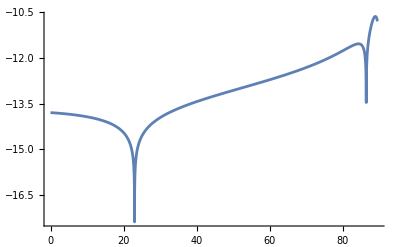

```mathematica
Plot[Log10[Abs[Vzz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r]]],{ϕ0,0,90-dθ/2}]
```

```mathematica
Export["vref_lat0.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1/12;
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2  * Pi / 180,prc];
ϕ0=SetPrecision[{80,961/12,481/6,321/4,241/3,965/12,161/2,967/12,242/3,323/4,485/6,971/12,81,973/12,487/6,325/4,244/3,977/12,163/2,979/12,245/3,327/4,491/6,983/12,82,985/12,493/6,329/4,247/3,989/12,165/2,991/12,248/3,331/4,497/6,995/12,83,997/12,499/6,333/4,250/3,1001/12,167/2,1003/12,251/3,335/4,503/6,1007/12,84,1009/12,505/6,337/4,253/3,1013/12,169/2,1015/12,254/3,339/4,509/6,1019/12,85,1021/12,511/6,341/4,256/3,1025/12,171/2,1027/12,257/3,343/4,515/6,1031/12,86,1033/12,517/6,345/4,259/3,1037/12,173/2,1039/12,260/3,347/4,521/6,1043/12,87,1045/12,523/6,349/4,262/3,1049/12,175/2,1051/12,263/3,351/4,527/6,1055/12,88,1057/12,529/6,353/4,265/3,1061/12,177/2,1063/12,266/3,355/4,533/6,1067/12,89,1069/12,535/6,357/4,268/3,1073/12,179/2,1075/12,269/3,359/4,539/6,1079/12,90-dθ/2},prc];

v = V[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vz = Vz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vzz = Vzz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vxx = Vxx[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vyy = Vyy[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vzzz = Vzzz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vxxz = Vxxz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
vyyz = Vyyz[r1,r2,(90-ϕ0-dθ/2 )*Pi / 180,(90-ϕ0+dθ/2 )*Pi / 180,λ1,λ2,r];
```

```mathematica
Export["vref_lat0_zm.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1/12;
θ1=SetPrecision[(θ0-dθ/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+dθ/2) * Pi / 180,prc];
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2 * Pi / 180,prc];
```

```mathematica
r=SetPrecision[r2+{10,10000,20000,30000,40000,50000,60000,70000,80000,90000,100000,110000,120000,130000,140000,150000,160000,170000,180000,190000,200000,210000,220000,230000,240000,250000,260000,270000,280000,290000,300000,310000,320000,330000,340000,350000,360000,370000,380000,390000,400000,410000,420000,430000,440000,450000,460000,470000,480000,490000,500000},prc];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_h_1_12.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1;
θ1=SetPrecision[(θ0-dθ/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+dθ/2) * Pi / 180,prc];
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2 * Pi / 180,prc];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_h_1.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1;
θ1=SetPrecision[(θ0-dθ/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+dθ/2) * Pi / 180,prc];
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2 * Pi / 180,prc];
h=260000;
r = r2 + h;
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_1_h_260000.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
h=10000;
r = r2 + h;
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_1_h_10000.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
h=10;
r = r2 + h;
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["D:/Paper/tesseroid-sh/sub1/data/vref_1_h_10.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
dθ=1/12;
θ1=SetPrecision[(θ0-dθ/2)* Pi / 180,prc];
θ2= SetPrecision[(θ0+dθ/2) * Pi / 180,prc];
λ1=SetPrecision[-dθ/2 * Pi / 180,prc];
λ2=SetPrecision[dθ/2 * Pi / 180,prc];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_12_h_10.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
h=10000;
r = r2 + h;
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_12_h_10000.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```

```mathematica
h=260000;
r=r2+h;
```

```mathematica
v = V[r1,r2,θ1,θ2,λ1,λ2,r];
vz = Vz[r1,r2,θ1,θ2,λ1,λ2,r];
vzz = Vzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxx = Vxx[r1,r2,θ1,θ2,λ1,λ2,r];
vyy = Vyy[r1,r2,θ1,θ2,λ1,λ2,r];
vzzz = Vzzz[r1,r2,θ1,θ2,λ1,λ2,r];
vxxz = Vxxz[r1,r2,θ1,θ2,λ1,λ2,r];
vyyz = Vyyz[r1,r2,θ1,θ2,λ1,λ2,r];
```

```mathematica
Export["vref_12_h_260000.mat",{"v_ref"->N[v,16],"vz_ref"->N[vz,16],"vzz_ref"->N[vzz,16],"vxx_ref"->N[vxx,16],"vyy_ref"->N[vyy,16],"vzzz_ref"->N[vzzz,16],"vxxz_ref"->N[vxxz,16],"vyyz_ref"->N[vyyz,16]},"MAT"];
```